## Alpha Beat

同样需要用到 yxlllc 所开发的编译器

```mathematica
Music[s_]:=MusicCreate@SMSPCompile[StringJoin["m[4,120,0]
<chords.txt\n z[1,3>\n",s],"CChordExtend"->True,"Directory"->"E:/"]
```

一些工具函数

```mathematica
(* 重复 *)
r[s_,time_]:=StringJoin[Table[s,{time}]]
```

### 定义一套架子鼓

```mathematica
M="BassDrum2"; (* 底鼓 *)
S="Snare"; (* 军鼓 *)

(* 嗵嗵鼓 *)
lT="LowTom";  
mT="MidTom"; 
nT="MidTom2"; 
hT="HighTom"; 

T="HiHatClosed"; (* 闭镲 *)
To="HiHatOpen"; (* 开镲 *)
Tc="CrashCymbal"; (* 吊镲 *)
```

反面例子：全部打在正拍

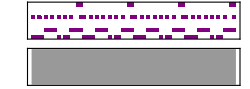

```mathematica
Music["[drum] i[Midi[]] v[.5]
[hat] i[Midi[]] v[.3]
[drum] |0] "<>r["M S M= 0= M_ S_ S_|",4]<>"
[hat] |0] "<>r[{r["T= 0= ",7],"To=` T= &|"},4]]
```

打一些在反拍上

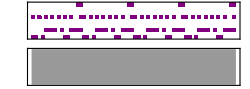

```mathematica
Music["[drum] i[Midi[]] v[.5]
[hat] i[Midi[]] v[.3]
[drum] |0] "<>r["M= M= 0= M= S 0= S= M_ S_ S_|",4]<>"
[hat] |0] "<>r[{r["T= 0= ",7],"To=` T= &|"},4]]
```

奇偶段末尾不同（加花）

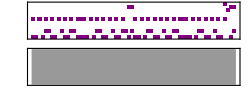

```mathematica
Music["[drum] i[Midi[]] v[.5]
[hat] i[Midi[]] v[.3]
[drum] |0] "<>StringJoin[
"M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M= M= 0= M= S_ M_ 0= S= M_ S= S= M= S=|",
"M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M= M= 0= M= S_ M_ 0= S= M_ mT= lT= M= S=|"
]<>"
[hat] |0] "<>r[{r["T= 0= ",7],"T= T= |",r["T= 0= ",7],"To_ |"},2]]
```

结尾单独加嗵嗵鼓

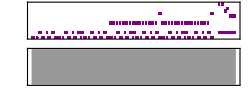

```mathematica
Music["[drum] i[Midi[]] v[.5]
[tom] i[Midi[]] v[.4]
[hat] i[Midi[]] v[.3]
[drum] |0] "<>StringJoin[
r["M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |"<>
"M= M= 0= M= S_ M_ 0= S= M_ S= S= M= S=|",3],
"M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |",
"0_= S_ S_ S= S_ S|"
]<>"
[hat] |3] "<>r[{r["T= 0= ",7],"T= T= |",r["T= 0= ",7],"To_ |"},2]<>"\n[tom] |7] 0_= hT= 0= hT= 0= mT= nT= 0= lT"]
```

函数封装，接收参数：drum、hat、tom（分别带起始小节号）

```mathematica
Beat[nd_,d_,nh_,h_,nt_,t_]:=StringJoin["\n
[drum] i[Midi[]] v[.5]
[tom] i[Midi[]] v[.4]
[hat] i[Midi[]] v[.3]
[drum] |",ToString[nd],"] ",d,"
[hat] |",ToString[nh],"] ",h,"\n[tom] |",ToString[nt],"] ",t]
```

### 底鼓复制到 bass

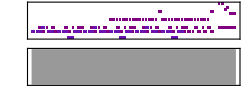

```mathematica
Music[{Beat[0,StringJoin[
r["M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |"<>
"M= M= 0= M= S_ M_ 0= S= M_ S= S= M= S=|",3],
"M= M= 0= M= S_ M_ 0= S= M_ S_ M_ |",
"0_= S_ S_ S= S_ S|"
],3,r[{r["T= 0= ",7],"T= T= |",r["T= 0= ",7],"To_ |"},2],7,"0_= hT= 0= hT= 0= mT= nT= 0= lT |"],
"[bass] i[Midi[Bass,-24]] v[.5]
[bass] |0] "<>r["1= 1= 0= 1=_ 2_ 0_ 1 |"<>
"1= 1= 0= 1=_ !6 1|",3]
}]
```

谱子配合织体

```mathematica
BassR[cp_,start_,ripat_]:=Module[{l=ChordPro[cp,start],righ},
l⟦All,3;;(2+Length[start])⟧=l⟦All,3;;(2+Length[start])⟧-12; (* 右手谱降八度 *)
righ=StringJoin[Table[{
StringReplace[ToString[l⟦i,1;;(2+Length[start])⟧],{" "->"","{"->"[","}"->"> "}],
ripat},{i,1,Length[cp]}]];
Return["[bass] i[Midi[Bass,-12]] v[1]
[bass] |0] "<>righ<>"\n"]
]
```

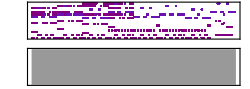

```mathematica
Music[{PianoLR[{4,5,3,6},{3,4,5},"s 0_= b= 0= b= 0_ b | ","s s z=+ 0= a= b= 0= s_= | "],
Beat[0,StringJoin[
r["M_ 0= M= S_ M_ 0= S= M_ S_ M_ |"<>
"M_ 0= M= S_ M_ 0= S= M_ S= S= M= S=|",3],
"M_ 0= M= S_ M_ 0= S= M_ S_ M_ |",
"0_= S_ S_ S= S_ S|"
],3,r[{r["T= 0= ",7],"T= T= |",r["T= 0= ",7],"To_ |"},2],7,"0_= hT= 0= hT= 0= mT= nT= 0= lT |"],
BassR[{4,5,3,6,4,5,3,6},{3,4,5},"a b_ a_ c=+ 0= b= a_ a_= | "]
}]
```